```mathematica
Nx=15;
Ny=15;
nx=15;
ny=15;
coulombvaldat={0,0.3,0.5,0.7,1,1.3,1.55,1.75,1.95,2,2.2,2.5,2.6,2.8,3,3.2,3.6,4};
```

```mathematica
momentax=Table[Total[Flatten[ Import[StringJoin["Us1_",ToString[coulombval],"_allmtax.dat"]][[1]][[{1,5,9}]]]],{coulombval,coulombvaldat}];
momentbx=Table[Total[Flatten[ Import[StringJoin["Us1_",ToString[coulombval],"_allmtbx.dat"]][[1]][[{1,5,9}]]]],{coulombval,coulombvaldat}];


mgdata=Table[{coulombvaldat[[i]],((momentax+momentbx)/2)[[i]]},{i,1,Length[coulombvaldat]}];
```

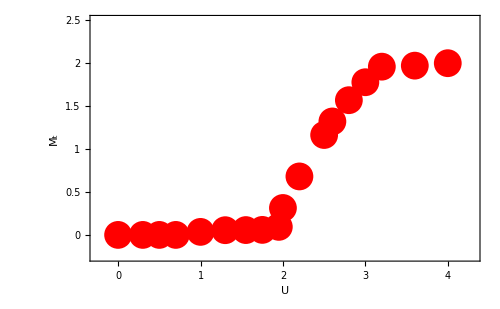

```mathematica
mgplot=ListPlot[mgdata,Frame->True,FrameStyle->Directive[Thickness[0.005],Black,32],Epilog->{{Red,PointSize[0.04],Point[mgdata]}},PlotRange->{{-0.25,4.3},{-0.25,2.5}},
FrameTicks->{{{{0,0,0.03},{0.5,0.5,0.03},{1,1,0.03},{1.5,1.5,0.03},{2,2,0.03},{2.5,2.5,0.03}},{{0,Null,0.03},{0.5,Null,0.03},{1,Null,0.03},{1.5,Null,0.03},{2,Null,0.03},{2.5,Null,0.03}}},{{{0,0,0.03},{1,1,0.03},{2,2,0.03},{3,3,0.03},{4,4,0.03}},{{0,Null,0.03},{1,Null,0.03},{2,Null,0.03},{3,Null,0.03},{4,Null,0.03}}}},
FrameLabel->{{Style["M_t",35,FontFamily->"TimesNewRoman"],None},{Style["U",35,FontFamily->"TimesNewRoman"],None}},
LabelStyle->{FontFamily->"TimesNewRoman",Directive[Black,35]},
ImagePadding->{{90,15},{90,17}},ImageSize->500]
Export["mgplot.eps",mgplot];
```